```mathematica
(*Evaluate conditions for resonant driving for an NV-14N-13C System*)
(*AN and AC are the parallel components of the hyperfine tensor in units of MHz*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*These equations are all conditions for the driving field strength B1, thus they all have to be equal, f1=f2=f3=f4=f5. l denotes the integer for the rotation of the electron spin. If uneven, we perform a NOT, if even, the phase kickback of the full rotation may be used as a logical CNOT between the 14N and 13C spin.*)
```

```mathematica
f1[l_]:=Sqrt[(AN^2*n^2)/(4*l^2-n^2)] (*AN,l*)
f2[q_]:=Sqrt[((2*AN)^2*n^2)/(4*q^2-n^2)](*2AN,q*)
f3[m_]:=Sqrt[(AC^2*n^2)/(4*m^2-n^2)](*AC,m*)
f4[k_]:=Sqrt[((AN+AC)^2*n^2)/(4*k^2-n^2)](*AN+AC,k*)
f5[p_]:=Sqrt[((2*AN+AC)^2*n^2)/(4*p^2-n^2)](*2AN+AC,p*)
```

```mathematica
StringForm["AN,l"]
t1=N[Table[{f1[r],r},{r,1,50}]]/.{AN->2.16,AC->0.43,n->1}

StringForm["2AN,q"]
t2=N[Table[{f2[r],r},{r,1,100}]]/.{AN->2.16,AC->0.43,n->1}

StringForm["AC,m"]
t3=N[Table[{f3[r],r},{r,1,100}]]/.{AN->2.16,AC->0.43,n->1}

StringForm["AC+AN,k"]
t4=N[Table[{f4[r],r},{r,1,100}]]/.{AN->2.16,AC->0.43,n->1}

StringForm["2AN+AC,p"]
t5=N[Table[{f5[r],r},{r,1,100}]]/.{AN->2.16,AC->0.43,n->1}
```

AN,l

{{1.24708,1.},{0.55771,2.},{0.365107,3.},{0.272134,4.},{0.217088,5.},{0.180628,6.},{0.154681,7.},{0.135264,8.},{0.120186,9.},{0.108135,10.},{0.0982834,11.},{0.0900782,12.},{0.0831384,13.},{0.0771921,14.},{0.07204,15.},{0.067533,16.},{0.0635569,17.},{0.0600232,18.},{0.0568618,19.},{0.0540169,20.},{0.0514432,21.},{0.0491036,22.},{0.0469676,23.},{0.0450098,24.},{0.0432086,25.},{0.0415461,26.},{0.0400069,27.},{0.0385776,28.},{0.0372469,29.},{0.036005,30.},{0.0348432,31.},{0.0337541,32.},{0.032731,33.},{0.0317681,34.},{0.0308603,35.},{0.0300029,36.},{0.0291919,37.},{0.0284235,38.},{0.0276946,39.},{0.0270021,40.},{0.0263434,41.},{0.0257161,42.},{0.025118,43.},{0.024547,44.},{0.0240015,45.},{0.0234796,46.},{0.02298,47.},{0.0225012,48.},{0.022042,49.},{0.0216011,50.}}

2AN,q

{{2.49415,1.},{1.11542,2.},{0.730213,3.},{0.544269,4.},{0.434176,5.},{0.361257,6.},{0.309362,7.},{0.270529,8.},{0.240371,9.},{0.216271,10.},{0.196567,11.},{0.180156,12.},{0.166277,13.},{0.154384,14.},{0.14408,15.},{0.135066,16.},{0.127114,17.},{0.120046,18.},{0.113724,19.},{0.108034,20.},{0.102886,21.},{0.0982072,22.},{0.0939352,23.},{0.0900195,24.},{0.0864173,25.},{0.0830923,26.},{0.0800137,27.},{0.0771552,28.},{0.0744938,29.},{0.07201,30.},{0.0696865,31.},{0.0675082,32.},{0.0654621,33.},{0.0635363,34.},{0.0617206,35.},{0.0600058,36.},{0.0583837,37.},{0.056847,38.},{0.0553892,39.},{0.0540042,40.},{0.0526868,41.},{0.0514322,42.},{0.050236,43.},{0.0490941,44.},{0.048003,45.},{0.0469593,46.},{0.04596,47.},{0.0450024,48.},{0.0440839,49.},{0.0432022,50.},{0.042355,51.},{0.0415404,52.},{0.0407565,53.},{0.0400017,54.},{0.0392744,55.},{0.038573,56.},{0.0378962,57.},{0.0372428,58.},{0.0366115,59.},{0.0360013,60.},{0.035411,61.},{0.0348398,62.},{0.0342868,63.},{0.033751,64.},{0.0332318,65.},{0.0327282,66.},{0.0322397,67.},{0.0317656,68.},{0.0313052,69.},{0.0308579,70.},{0.0304233,71.},{0.0300007,72.},{0.0295897,73.},{0.0291899,74.},{0.0288006,75.},{0.0284217,76.},{0.0280525,77.},{0.0276929,78.},{0.0273423,79.},{0.0270005,80.},{0.0266672,81.},{0.026342,82.},{0.0260246,83.},{0.0257147,84.},{0.0254122,85.},{0.0251167,86.},{0.024828,87.},{0.0245459,88.},{0.02427,89.},{0.0240004,90.},{0.0237366,91.},{0.0234786,92.},{0.0232261,93.},{0.022979,94.},{0.0227372,95.},{0.0225003,96.},{0.0222683,97.},{0.0220411,98.},{0.0218185,99.},{0.0216003,100.}}

AC,m

{{0.248261,1.},{0.111026,2.},{0.0726833,3.},{0.0541749,4.},{0.0432166,5.},{0.0359584,6.},{0.0307929,7.},{0.0269276,8.},{0.0239258,9.},{0.0215269,10.},{0.0195657,11.},{0.0179322,12.},{0.0165507,13.},{0.0153669,14.},{0.0143413,15.},{0.0134441,16.},{0.0126525,17.},{0.0119491,18.},{0.0113197,19.},{0.0107534,20.},{0.010241,21.},{0.00977525,22.},{0.00935004,23.},{0.00896028,24.},{0.00860172,25.},{0.00827076,26.},{0.00796433,27.},{0.0076798,28.},{0.0074149,29.},{0.00716766,30.},{0.00693639,31.},{0.00671957,32.},{0.0065159,33.},{0.00632421,34.},{0.00614348,35.},{0.0059728,36.},{0.00581134,37.},{0.00565838,38.},{0.00551327,39.},{0.00537542,40.},{0.00524429,41.},{0.00511941,42.},{0.00500034,43.},{0.00488668,44.},{0.00477807,45.},{0.00467419,46.},{0.00457473,47.},{0.00447941,48.},{0.00438798,49.},{0.00430022,50.},{0.00421589,51.},{0.00413481,52.},{0.00405678,53.},{0.00398165,54.},{0.00390925,55.},{0.00383944,56.},{0.00377207,57.},{0.00370703,58.},{0.0036442,59.},{0.00358346,60.},{0.00352471,61.},{0.00346785,62.},{0.00341281,63.},{0.00335948,64.},{0.00330779,65.},{0.00325767,66.},{0.00320904,67.},{0.00316185,68.},{0.00311602,69.},{0.00307151,70.},{0.00302824,71.},{0.00298618,72.},{0.00294527,73.},{0.00290547,74.},{0.00286673,75.},{0.00282901,76.},{0.00279227,77.},{0.00275647,78.},{0.00272157,79.},{0.00268755,80.},{0.00265437,81.},{0.002622,82.},{0.00259041,83.},{0.00255957,84.},{0.00252946,85.},{0.00250004,86.},{0.00247131,87.},{0.00244322,88.},{0.00241577,89.},{0.00238893,90.},{0.00236267,91.},{0.00233699,92.},{0.00231186,93.},{0.00228727,94.},{0.00226319,95.},{0.00223961,96.},{0.00221652,97.},{0.00219391,98.},{0.00217174,99.},{0.00215003,100.}}

AC+AN,k

{{1.49534,1.},{0.668735,2.},{0.43779,3.},{0.326309,4.},{0.260305,5.},{0.216587,6.},{0.185474,7.},{0.162192,8.},{0.144111,9.},{0.129662,10.},{0.117849,11.},{0.10801,12.},{0.0996891,13.},{0.092559,14.},{0.0863813,15.},{0.080977,16.},{0.0762094,17.},{0.0719722,18.},{0.0681815,19.},{0.0647702,20.},{0.0616842,21.},{0.0588788,22.},{0.0563177,23.},{0.05397,24.},{0.0518104,25.},{0.0498169,26.},{0.0479712,27.},{0.0462574,28.},{0.0446618,29.},{0.0431727,30.},{0.0417796,31.},{0.0404737,32.},{0.0392469,33.},{0.0380924,34.},{0.0370038,35.},{0.0359757,36.},{0.0350032,37.},{0.0340819,38.},{0.0332079,39.},{0.0323775,40.},{0.0315877,41.},{0.0308355,42.},{0.0301183,43.},{0.0294337,44.},{0.0287796,45.},{0.0281538,46.},{0.0275548,47.},{0.0269806,48.},{0.0264299,49.},{0.0259013,50.},{0.0253934,51.},{0.024905,52.},{0.024435,53.},{0.0239825,54.},{0.0235464,55.},{0.0231259,56.},{0.0227202,57.},{0.0223284,58.},{0.0219499,59.},{0.0215841,60.},{0.0212302,61.},{0.0208878,62.},{0.0205562,63.},{0.020235,64.},{0.0199237,65.},{0.0196218,66.},{0.0193289,67.},{0.0190446,68.},{0.0187686,69.},{0.0185005,70.},{0.0182399,71.},{0.0179865,72.},{0.0177401,73.},{0.0175004,74.},{0.0172671,75.},{0.0170398,76.},{0.0168185,77.},{0.0166029,78.},{0.0163927,79.},{0.0161878,80.},{0.015988,81.},{0.015793,82.},{0.0156027,83.},{0.0154169,84.},{0.0152356,85.},{0.0150584,86.},{0.0148853,87.},{0.0147161,88.},{0.0145508,89.},{0.0143891,90.},{0.014231,91.},{0.0140763,92.},{0.0139249,93.},{0.0137768,94.},{0.0136318,95.},{0.0134898,96.},{0.0133507,97.},{0.0132145,98.},{0.013081,99.},{0.0129502,100.}}

2AN+AC,p

{{2.74241,1.},{1.22644,2.},{0.802897,3.},{0.598444,4.},{0.477393,5.},{0.397215,6.},{0.340155,7.},{0.297457,8.},{0.264297,9.},{0.237797,10.},{0.216132,11.},{0.198089,12.},{0.182828,13.},{0.169751,14.},{0.158421,15.},{0.14851,16.},{0.139766,17.},{0.131995,18.},{0.125043,19.},{0.118787,20.},{0.113127,21.},{0.107982,22.},{0.103285,23.},{0.0989798,24.},{0.095019,25.},{0.091363,26.},{0.087978,27.},{0.084835,28.},{0.0819087,29.},{0.0791777,30.},{0.0766229,31.},{0.0742278,32.},{0.071978,33.},{0.0698605,34.},{0.0678641,35.},{0.0659786,36.},{0.0641951,37.},{0.0625054,38.},{0.0609024,39.},{0.0593796,40.},{0.0579311,41.},{0.0565516,42.},{0.0552363,43.},{0.0539808,44.},{0.052781,45.},{0.0516335,46.},{0.0505348,47.},{0.0494819,48.},{0.0484719,49.},{0.0475024,50.},{0.0465709,51.},{0.0456752,52.},{0.0448133,53.},{0.0439834,54.},{0.0431836,55.},{0.0424124,56.},{0.0416683,57.},{0.0409498,58.},{0.0402557,59.},{0.0395847,60.},{0.0389357,61.},{0.0383077,62.},{0.0376996,63.},{0.0371105,64.},{0.0365395,65.},{0.0359859,66.},{0.0354487,67.},{0.0349274,68.},{0.0344212,69.},{0.0339294,70.},{0.0334515,71.},{0.0329869,72.},{0.032535,73.},{0.0320953,74.},{0.0316674,75.},{0.0312507,76.},{0.0308448,77.},{0.0304493,78.},{0.0300639,79.},{0.0296881,80.},{0.0293215,81.},{0.028964,82.},{0.028615,83.},{0.0282743,84.},{0.0279417,85.},{0.0276167,86.},{0.0272993,87.},{0.0269891,88.},{0.0266858,89.},{0.0263893,90.},{0.0260993,91.},{0.0258156,92.},{0.025538,93.},{0.0252663,94.},{0.0250003,95.},{0.0247399,96.},{0.0244849,97.},{0.024235,98.},{0.0239902,99.},{0.0237503,100.}}

```mathematica
(*Also ist das Vorgehen hier: der größtmögliche Wert für B1 ist durch Gleichung f3 gegeben. Also von hier abwärts mit der gewünschten numerischen Genauigkeit durch die Listen gehen und sehen, ob der Wert in allen Listen vorhanden ist. Gibt es eine bessere Lösung?*)
```

```mathematica
localMax1=FindMaximum[{Fav/.{m->3,k->18,p->33,q->30,l->15},0.068<=b1<=0.073},{b1,0.072}]
localMax2=FindMaximum[{Fav/.{m->4,k->24,p->44,q->40,l->20},0.051<=b1<=0.058},{b1,0.054}]
localMax3=FindMaximum[{Fav/.{m->5,k->30,p->55,q->50,l->25},0.041<=b1<=0.045},{b1,0.043}]
localMax3=FindMaximum[{Fav/.{m->6,k->36,p->66,q->60,l->30},0.035<=b1<=0.037},{b1,0.036}]
```

{0.998488,{b1→0.0719964}}

{0.999205,{b1→0.0539915}}

{0.999195,{b1→0.0431911}}

{0.998821,{b1→0.0359916}}

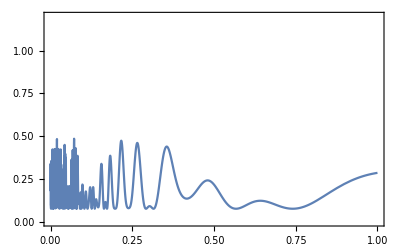

```mathematica
Fav=F/.{AN->2.16,AC->0.43,n->1};
Plot[{Fav},{b1,0.0,1},PlotRange->{0,1.2},Frame->True]
```

```mathematica
StringForm["AN,l"]
t1=N[Table[{f1[r],r},{r,2,50}]]/.{AN->2.16,AC->0.43,n->2}

StringForm["2AN,q"]
t2=N[Table[{f2[r],r},{r,2,100}]]/.{AN->2.16,AC->0.43,n->2}

StringForm["AC,m"]
t3=N[Table[{f3[r],r},{r,2,100}]]/.{AN->2.16,AC->0.43,n->2}

StringForm["AC+AN,k"]
t4=N[Table[{f4[r],r},{r,2,100}]]/.{AN->2.16,AC->0.43,n->2}

StringForm["2AN+AC,p"]
t5=N[Table[{f5[r],r},{r,2,100}]]/.{AN->2.16,AC->0.43,n->2}
```

AN,l

{{1.24708,2.},{0.763675,3.},{0.55771,4.},{0.440908,5.},{0.365107,6.},{0.311769,7.},{0.272134,8.},{0.241495,9.},{0.217088,10.},{0.19718,11.},{0.180628,12.},{0.166648,13.},{0.154681,14.},{0.144321,15.},{0.135264,16.},{0.127279,17.},{0.120186,18.},{0.113842,19.},{0.108135,20.},{0.102974,21.},{0.0982834,22.},{0.0940019,23.},{0.0900782,24.},{0.0864692,25.},{0.0831384,26.},{0.0800549,27.},{0.0771921,28.},{0.0745271,29.},{0.07204,30.},{0.0697137,31.},{0.067533,32.},{0.0654846,33.},{0.0635569,34.},{0.0617395,35.},{0.0600232,36.},{0.0583997,37.},{0.0568618,38.},{0.0554028,39.},{0.0540169,40.},{0.0526986,41.},{0.0514432,42.},{0.0502461,43.},{0.0491036,44.},{0.0480119,45.},{0.0469676,46.},{0.0459679,47.},{0.0450098,48.},{0.0440908,49.},{0.0432086,50.}}

2AN,q

{{2.49415,2.},{1.52735,3.},{1.11542,4.},{0.881816,5.},{0.730213,6.},{0.623538,7.},{0.544269,8.},{0.482991,9.},{0.434176,10.},{0.39436,11.},{0.361257,12.},{0.333295,13.},{0.309362,14.},{0.288642,15.},{0.270529,16.},{0.254558,17.},{0.240371,18.},{0.227684,19.},{0.216271,20.},{0.205948,21.},{0.196567,22.},{0.188004,23.},{0.180156,24.},{0.172938,25.},{0.166277,26.},{0.16011,27.},{0.154384,28.},{0.149054,29.},{0.14408,30.},{0.139427,31.},{0.135066,32.},{0.130969,33.},{0.127114,34.},{0.123479,35.},{0.120046,36.},{0.116799,37.},{0.113724,38.},{0.110806,39.},{0.108034,40.},{0.105397,41.},{0.102886,42.},{0.100492,43.},{0.0982072,44.},{0.0960237,45.},{0.0939352,46.},{0.0919357,47.},{0.0900195,48.},{0.0881816,49.},{0.0864173,50.},{0.0847222,51.},{0.0830923,52.},{0.0815239,53.},{0.0800137,54.},{0.0785584,55.},{0.0771552,56.},{0.0758011,57.},{0.0744938,58.},{0.0732309,59.},{0.07201,60.},{0.0708292,61.},{0.0696865,62.},{0.0685801,63.},{0.0675082,64.},{0.0664694,65.},{0.0654621,66.},{0.0644848,67.},{0.0635363,68.},{0.0626153,69.},{0.0617206,70.},{0.0608511,71.},{0.0600058,72.},{0.0591836,73.},{0.0583837,74.},{0.0576051,75.},{0.056847,76.},{0.0561086,77.},{0.0553892,78.},{0.0546879,79.},{0.0540042,80.},{0.0533374,81.},{0.0526868,82.},{0.052052,83.},{0.0514322,84.},{0.050827,85.},{0.050236,86.},{0.0496585,87.},{0.0490941,88.},{0.0485424,89.},{0.048003,90.},{0.0474754,91.},{0.0469593,92.},{0.0464543,93.},{0.04596,94.},{0.0454762,95.},{0.0450024,96.},{0.0445384,97.},{0.0440839,98.},{0.0436386,99.},{0.0432022,100.}}

AC,m

{{0.248261,2.},{0.152028,3.},{0.111026,4.},{0.0877734,5.},{0.0726833,6.},{0.0620652,7.},{0.0541749,8.},{0.0480755,9.},{0.0432166,10.},{0.0392534,11.},{0.0359584,12.},{0.0331752,13.},{0.0307929,14.},{0.0287306,15.},{0.0269276,16.},{0.025338,17.},{0.0239258,18.},{0.022663,19.},{0.0215269,20.},{0.0204994,21.},{0.0195657,22.},{0.0187133,23.},{0.0179322,24.},{0.0172138,25.},{0.0165507,26.},{0.0159369,27.},{0.0153669,28.},{0.0148364,29.},{0.0143413,30.},{0.0138782,31.},{0.0134441,32.},{0.0130363,33.},{0.0126525,34.},{0.0122907,35.},{0.0119491,36.},{0.0116259,37.},{0.0113197,38.},{0.0110293,39.},{0.0107534,40.},{0.0104909,41.},{0.010241,42.},{0.0100027,43.},{0.00977525,44.},{0.00955792,45.},{0.00935004,46.},{0.00915101,47.},{0.00896028,48.},{0.00877734,49.},{0.00860172,50.},{0.00843299,51.},{0.00827076,52.},{0.00811465,53.},{0.00796433,54.},{0.00781947,55.},{0.0076798,56.},{0.00754502,57.},{0.0074149,58.},{0.00728918,59.},{0.00716766,60.},{0.00705013,61.},{0.00693639,62.},{0.00682626,63.},{0.00671957,64.},{0.00661617,65.},{0.0065159,66.},{0.00641863,67.},{0.00632421,68.},{0.00623254,69.},{0.00614348,70.},{0.00605694,71.},{0.0059728,72.},{0.00589096,73.},{0.00581134,74.},{0.00573384,75.},{0.00565838,76.},{0.00558489,77.},{0.00551327,78.},{0.00544347,79.},{0.00537542,80.},{0.00530905,81.},{0.00524429,82.},{0.0051811,83.},{0.00511941,84.},{0.00505917,85.},{0.00500034,86.},{0.00494286,87.},{0.00488668,88.},{0.00483177,89.},{0.00477807,90.},{0.00472556,91.},{0.00467419,92.},{0.00462392,93.},{0.00457473,94.},{0.00452657,95.},{0.00447941,96.},{0.00443323,97.},{0.00438798,98.},{0.00434366,99.},{0.00430022,100.}}

AC+AN,k

{{1.49534,2.},{0.915703,3.},{0.668735,4.},{0.528682,5.},{0.43779,6.},{0.373834,7.},{0.326309,8.},{0.289571,9.},{0.260305,10.},{0.236434,11.},{0.216587,12.},{0.199823,13.},{0.185474,14.},{0.173052,15.},{0.162192,16.},{0.152617,17.},{0.144111,18.},{0.136505,19.},{0.129662,20.},{0.123473,21.},{0.117849,22.},{0.112715,23.},{0.10801,24.},{0.103683,25.},{0.0996891,26.},{0.0959918,27.},{0.092559,28.},{0.0893635,29.},{0.0863813,30.},{0.0835919,31.},{0.080977,32.},{0.0785209,33.},{0.0762094,34.},{0.0740302,35.},{0.0719722,36.},{0.0700256,37.},{0.0681815,38.},{0.0664321,39.},{0.0647702,40.},{0.0631895,41.},{0.0616842,42.},{0.0602489,43.},{0.0588788,44.},{0.0575698,45.},{0.0563177,46.},{0.0551189,47.},{0.05397,48.},{0.0528682,49.},{0.0518104,50.},{0.0507941,51.},{0.0498169,52.},{0.0488766,53.},{0.0479712,54.},{0.0470987,55.},{0.0462574,56.},{0.0454456,57.},{0.0446618,58.},{0.0439046,59.},{0.0431727,60.},{0.0424647,61.},{0.0417796,62.},{0.0411163,63.},{0.0404737,64.},{0.0398509,65.},{0.0392469,66.},{0.038661,67.},{0.0380924,68.},{0.0375402,69.},{0.0370038,70.},{0.0364825,71.},{0.0359757,72.},{0.0354828,73.},{0.0350032,74.},{0.0345364,75.},{0.0340819,76.},{0.0336392,77.},{0.0332079,78.},{0.0327874,79.},{0.0323775,80.},{0.0319777,81.},{0.0315877,82.},{0.0312071,83.},{0.0308355,84.},{0.0304727,85.},{0.0301183,86.},{0.0297721,87.},{0.0294337,88.},{0.029103,89.},{0.0287796,90.},{0.0284633,91.},{0.0281538,92.},{0.0278511,93.},{0.0275548,94.},{0.0272647,95.},{0.0269806,96.},{0.0267024,97.},{0.0264299,98.},{0.026163,99.},{0.0259013,100.}}

2AN+AC,p

{{2.74241,2.},{1.67938,3.},{1.22644,4.},{0.96959,5.},{0.802897,6.},{0.685603,7.},{0.598444,8.},{0.531066,9.},{0.477393,10.},{0.433614,11.},{0.397215,12.},{0.36647,13.},{0.340155,14.},{0.317373,15.},{0.297457,16.},{0.279896,17.},{0.264297,18.},{0.250347,19.},{0.237797,20.},{0.226447,21.},{0.216132,22.},{0.206717,23.},{0.198089,24.},{0.190152,25.},{0.182828,26.},{0.176047,27.},{0.169751,28.},{0.163891,29.},{0.158421,30.},{0.153306,31.},{0.14851,32.},{0.144006,33.},{0.139766,34.},{0.13577,35.},{0.131995,36.},{0.128425,37.},{0.125043,38.},{0.121835,39.},{0.118787,40.},{0.115888,41.},{0.113127,42.},{0.110495,43.},{0.107982,44.},{0.105582,45.},{0.103285,46.},{0.101087,47.},{0.0989798,48.},{0.096959,49.},{0.095019,50.},{0.0931552,51.},{0.091363,52.},{0.0896386,53.},{0.087978,54.},{0.0863779,55.},{0.084835,56.},{0.0833462,57.},{0.0819087,58.},{0.08052,59.},{0.0791777,60.},{0.0778793,61.},{0.0766229,62.},{0.0754063,63.},{0.0742278,64.},{0.0730856,65.},{0.071978,66.},{0.0709034,67.},{0.0698605,68.},{0.0688478,69.},{0.0678641,70.},{0.066908,71.},{0.0659786,72.},{0.0650746,73.},{0.0641951,74.},{0.063339,75.},{0.0625054,76.},{0.0616935,77.},{0.0609024,78.},{0.0601314,79.},{0.0593796,80.},{0.0586464,81.},{0.0579311,82.},{0.0572331,83.},{0.0565516,84.},{0.0558862,85.},{0.0552363,86.},{0.0546013,87.},{0.0539808,88.},{0.0533742,89.},{0.052781,90.},{0.052201,91.},{0.0516335,92.},{0.0510782,93.},{0.0505348,94.},{0.0500028,95.},{0.0494819,96.},{0.0489717,97.},{0.0484719,98.},{0.0479822,99.},{0.0475024,100.}}

```mathematica
FavCZ=FavRawCZ/.{AN->2.16,AC->0.43,n->2};
localMax7=FindMaximum[{FavCZ/.{m->3,k->17,p->31,q->28,l->14},0.14<=b1<=0.16},{b1,0.15}]
localMax8=FindMaximum[{FavCZ/.{m->5,k->30,p->55,q->50,l->25},0.079<=b1<=0.089},{b1,0.086}]
localMax9=FindMaximum[{FavCZ/.{m->6,k->36,p->66,q->60,l->30},0.070<=b1<=0.074},{b1,0.072}]
```

{0.933909,{b1→0.153712}}

{0.990137,{b1→0.0864049}}

{0.993967,{b1→0.0719964}}

```mathematica
F=1/13+1/39 Cos[m π]^2 Cos[(√(AC^2+b1^2) n π)/(2 b1)]^2+2/39 Cos[l π] Cos[m π] Cos[(√(AC^2+b1^2) n π)/(2 b1)] Cos[(√(AN^2+b1^2) n π)/(2 b1)]+1/39 Cos[l π]^2 Cos[(√(AN^2+b1^2) n π)/(2 b1)]^2+2/39 Cos[k π] Cos[m π] Cos[(√(AC^2+b1^2) n π)/(2 b1)] Cos[(√((AC+AN)^2+b1^2) n π)/(2 b1)]+2/39 Cos[k π] Cos[l π] Cos[(√(AN^2+b1^2) n π)/(2 b1)] Cos[(√((AC+AN)^2+b1^2) n π)/(2 b1)]+1/39 Cos[k π]^2 Cos[(√((AC+AN)^2+b1^2) n π)/(2 b1)]^2+2/39 Cos[m π] Cos[(√(AC^2+b1^2) n π)/(2 b1)] Cos[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)] Cos[p π]+2/39 Cos[l π] Cos[(√(AN^2+b1^2) n π)/(2 b1)] Cos[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)] Cos[p π]+2/39 Cos[k π] Cos[(√((AC+AN)^2+b1^2) n π)/(2 b1)] Cos[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)] Cos[p π]+1/39 Cos[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)]^2 Cos[p π]^2+2/39 Cos[m π] Cos[(√(AC^2+b1^2) n π)/(2 b1)] Cos[(√(4 AN^2+b1^2) n π)/(2 b1)] Cos[π q]+2/39 Cos[l π] Cos[(√(AN^2+b1^2) n π)/(2 b1)] Cos[(√(4 AN^2+b1^2) n π)/(2 b1)] Cos[π q]+2/39 Cos[k π] Cos[(√(4 AN^2+b1^2) n π)/(2 b1)] Cos[(√((AC+AN)^2+b1^2) n π)/(2 b1)] Cos[π q]+2/39 Cos[(√(4 AN^2+b1^2) n π)/(2 b1)] Cos[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)] Cos[p π] Cos[π q]+1/39 Cos[(√(4 AN^2+b1^2) n π)/(2 b1)]^2 Cos[π q]^2+1/39 Cos[(√((AC+AN)^2+b1^2) n π)/(2 b1)]^2 Sin[k π]^2+2/39 Cos[(√(AN^2+b1^2) n π)/(2 b1)] Cos[(√((AC+AN)^2+b1^2) n π)/(2 b1)] Sin[k π] Sin[l π]+1/39 Cos[(√(AN^2+b1^2) n π)/(2 b1)]^2 Sin[l π]^2+2/39 Cos[(√(AC^2+b1^2) n π)/(2 b1)] Cos[(√((AC+AN)^2+b1^2) n π)/(2 b1)] Sin[k π] Sin[m π]+2/39 Cos[(√(AC^2+b1^2) n π)/(2 b1)] Cos[(√(AN^2+b1^2) n π)/(2 b1)] Sin[l π] Sin[m π]+1/39 Cos[(√(AC^2+b1^2) n π)/(2 b1)]^2 Sin[m π]^2-2/39 Cos[m π] Cos[n π] Cos[(√(AC^2+b1^2) n π)/(2 b1)] Sin[(n π)/2]-2/39 Cos[l π] Cos[n π] Cos[(√(AN^2+b1^2) n π)/(2 b1)] Sin[(n π)/2]-2/39 Cos[k π] Cos[n π] Cos[(√((AC+AN)^2+b1^2) n π)/(2 b1)] Sin[(n π)/2]-2/39 Cos[n π] Cos[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)] Cos[p π] Sin[(n π)/2]-2/39 Cos[n π] Cos[(√(4 AN^2+b1^2) n π)/(2 b1)] Cos[π q] Sin[(n π)/2]+1/39 Cos[n π]^2 Sin[(n π)/2]^2-2/39 Cos[(√((AC+AN)^2+b1^2) n π)/(2 b1)] Sin[k π] Sin[(n π)/2] Sin[n π]-2/39 Cos[(√(AN^2+b1^2) n π)/(2 b1)] Sin[l π] Sin[(n π)/2] Sin[n π]-2/39 Cos[(√(AC^2+b1^2) n π)/(2 b1)] Sin[m π] Sin[(n π)/2] Sin[n π]+1/39 Sin[(n π)/2]^2 Sin[n π]^2+2/39 Cos[(√((AC+AN)^2+b1^2) n π)/(2 b1)] Cos[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)] Sin[k π] Sin[p π]+2/39 Cos[(√(AN^2+b1^2) n π)/(2 b1)] Cos[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)] Sin[l π] Sin[p π]+2/39 Cos[(√(AC^2+b1^2) n π)/(2 b1)] Cos[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)] Sin[m π] Sin[p π]-2/39 Cos[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)] Sin[(n π)/2] Sin[n π] Sin[p π]+1/39 Cos[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)]^2 Sin[p π]^2+2/39 Cos[(√(4 AN^2+b1^2) n π)/(2 b1)] Cos[(√((AC+AN)^2+b1^2) n π)/(2 b1)] Sin[k π] Sin[π q]+2/39 Cos[(√(AN^2+b1^2) n π)/(2 b1)] Cos[(√(4 AN^2+b1^2) n π)/(2 b1)] Sin[l π] Sin[π q]+2/39 Cos[(√(AC^2+b1^2) n π)/(2 b1)] Cos[(√(4 AN^2+b1^2) n π)/(2 b1)] Sin[m π] Sin[π q]-2/39 Cos[(√(4 AN^2+b1^2) n π)/(2 b1)] Sin[(n π)/2] Sin[n π] Sin[π q]+2/39 Cos[(√(4 AN^2+b1^2) n π)/(2 b1)] Cos[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)] Sin[p π] Sin[π q]+1/39 Cos[(√(4 AN^2+b1^2) n π)/(2 b1)]^2 Sin[π q]^2;
```

```mathematica
(*Ich muss einen Array machen mit der Gatterze{it und der Fidelity*)
```

```mathematica
val={{n*π/b1/.{n->1,b1->0.053991548418465936},0.9992054398007539},
{n*π/b1/.{n->1,b1->0.04319109823683413},0.9991947276789411 },
{n*π/b1/.{n->1,b1->0.07199641782880369} ,0.998487613470808},
{n*π/b1/.{n->1,b1->0.03599161161110898},0.998821232783512 },
{n*π/b1/.{n->2,b1->0.08640491408035118},0.9901365265355128 }}
```

{{58.1867,0.999205},{72.737,0.999195},{43.6354,0.998488},{87.2868,0.998821},{72.7179,0.990137}}

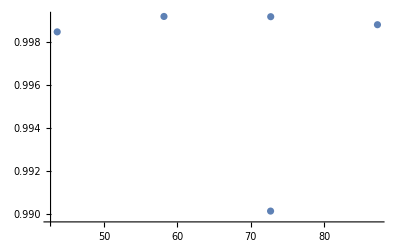

```mathematica
ListPlot[val]
```

```mathematica
Export["file6.dat",val,"Table"]
```

file6.dat